# ImStat

Statistics of image collection

## Setup and data collection

## Config

Source folder for JPG files:

```mathematica
imageDir="/media/superraid/images/images/";
```

Nr of raw files:

```mathematica
nrRawFiles=FileNames["*.CR2",imageDir,∞]//Length
```

9981

```mathematica
jpgFileNames=FileNames["*.jpg"|"*.JPG",imageDir,∞];
```

Number of images found:

```mathematica
nrJpgFiles=Length[jpgFileNames]
```

3955

Folder for local data storage:

```mathematica
dataDir=FileNameJoin[{NotebookDirectory[],"dataStorage"}]
```

/home/malte/dev/imStat/dataStorage

```mathematica
CreateDirectory[dataDir]
```

/home/malte/dev/imStat/dataStorage

## Retrieve mini JPG files and basic data

Compute data file name from original path, making sure that no collisions will occur:

```mathematica
(Union[Hash[#,"CRC32"]&/@jpgFileNames]//Length)==nrJpgFiles
```

True

```mathematica
storageFile[path_]:=FileNameJoin[{dataDir,ToString[Hash[path,"CRC32"]]<>".dst"}];
```

```mathematica
storageFileImg[path_]:=FileNameJoin[{dataDir,ToString[Hash[path,"CRC32"]]<>".jpg"}];
```

Fetch original image and save data into data file:

```mathematica
createData[path_]/;FileExistsQ[storageFile[path]]=Null;
```

```mathematica
createData[path_]:=Module[{img,dimensions,smallImg,aperture,bitDepth,orientation,colorSpace,date,exposure,focalLength,imageSize,iso,manufacturer,model,exifData},
exifData=Import[path,{{"Aperture","BitDepth","CameraTopOrientation","ColorSpace","Date","Exposure","FocalLength","ImageSize","ISOSpeed","Manufacturer","Model"}}];
If[!MatchQ[exifData,{_,_,_,_String,{_,_,_,_,_,_},_,_,{_,_},_,_String,_String}],
Return[$Failed];
];
img=Import[path];
dimensions=ImageDimensions[img];
smallImg=ImageResize[img,{300},Resampling->"Bilinear"];
Put[{dimensions,exifData},storageFile[path]];
Export[storageFileImg[path],smallImg];
]
```

File size:

```mathematica
fileSizes={#,FileByteCount[#]}&/@jpgFileNames;
```

```mathematica
Put[fileSizes,FileNameJoin[{dataDir,"fileSizes.dst"}]];
```

Retrieving file sizes:

```mathematica
fileSizes=Get[FileNameJoin[{dataDir,"fileSizes.dst"}]];
```

Fetch data in order of preference {memory, data file}:

```mathematica
ClearAll[getData];
getData[path_]/;FileExistsQ[storageFile[path]]:=getData[path]={Import[storageFileImg[path]],Get[storageFile[path]]}
```

```mathematica
getData[_]:=$Failed
```

Accessor functions for properties:

```mathematica
getData[path_,"Date"]:=getData[path][[2,2,5]]
```

```mathematica
getData[path_,"Orientation"]:=getData[path][[2,2,3]]
```

```mathematica
getData[path_,"Camera"]:=getData[path][[2,2,10;;11]]
```

## Retrieve image data

```mathematica
Monitor[
ParallelDo[createData[jpgFileNames[[i]]],{i,Length[jpgFileNames]}],
Refresh[
ProgressIndicator[Length@FileNames["*",dataDir],{0,2Length[jpgFileNames]}],
UpdateInterval->0.5,
TrackedSymbols->{}
]
]
```

Import::fmterr: Cannot import data as "JPEG" format.

General::stop: Further output of Import :: fmterr will be suppressed during this calculation.

Import::fmterr: Cannot import data as "JPEG" format.

General::stop: Further output of Import :: fmterr will be suppressed during this calculation.

Import::fmterr: Cannot import data as "JPEG" format.

General::stop: Further output of Import :: fmterr will be suppressed during this calculation.

Import::fmterr: Cannot import data as "JPEG" format.

General::stop: Further output of Import :: fmterr will be suppressed during this calculation.

```mathematica
goodFileNames=Select[jpgFileNames,FileExistsQ[storageFile[#]]&&FileExistsQ[storageFileImg[#]]&];
```

## Results

## Number of images taken

```mathematica
nrJpg=Length[jpgFileNames]
```

3955

```mathematica
nrGood=Length[goodFileNames]
```

3686

```mathematica
nrNotGood=nrJpg-nrGood
```

269

```mathematica
PieChart[{nrGood,nrNotGood},ChartLabels->{"","No data"}]
```

-Graphics-

## Images taken over time

```mathematica
getData[goodFileNames[[1]],"Date"]
```

{2007,12,23,17,14,56}

```mathematica
imageDates=Monitor[
Table[getData[goodFileNames[[i]],"Date"],{i,Length[goodFileNames]}],
Refresh[
ProgressIndicator[i,{0,Length[goodFileNames]}],
UpdateInterval->0.5,
TrackedSymbols->{}
]
];
```

```mathematica
oldestYear=Min@imageDates[[All,1]]
```

2006

```mathematica
newestYear=Max@imageDates[[All,1]]
```

2012

```mathematica
nrTakenTime=Join@@Table[{{y,m},Length@Cases[imageDates,{y,m,d_,h_,mi_,s_}]},{y,oldestYear,newestYear},{m,1,12}]
```

{{{2006,1},0},{{2006,2},0},{{2006,3},0},{{2006,4},0},{{2006,5},0},{{2006,6},0},{{2006,7},0},{{2006,8},0},{{2006,9},0},{{2006,10},0},{{2006,11},0},{{2006,12},6},{{2007,1},0},{{2007,2},8},{{2007,3},22},{{2007,4},138},{{2007,5},44},{{2007,6},42},{{2007,7},90},{{2007,8},41},{{2007,9},244},{{2007,10},170},{{2007,11},114},{{2007,12},166},{{2008,1},286},{{2008,2},202},{{2008,3},261},{{2008,4},91},{{2008,5},253},{{2008,6},190},{{2008,7},233},{{2008,8},429},{{2008,9},0},{{2008,10},2},{{2008,11},1},{{2008,12},26},{{2009,1},2},{{2009,2},3},{{2009,3},0},{{2009,4},20},{{2009,5},3},{{2009,6},5},{{2009,7},8},{{2009,8},0},{{2009,9},0},{{2009,10},6},{{2009,11},0},{{2009,12},2},{{2010,1},0},{{2010,2},0},{{2010,3},0},{{2010,4},0},{{2010,5},3},{{2010,6},0},{{2010,7},1},{{2010,8},1},{{2010,9},0},{{2010,10},7},{{2010,11},6},{{2010,12},1},{{2011,1},151},{{2011,2},0},{{2011,3},0},{{2011,4},249},{{2011,5},10},{{2011,6},9},{{2011,7},1},{{2011,8},0},{{2011,9},3},{{2011,10},35},{{2011,11},0},{{2011,12},0},{{2012,1},0},{{2012,2},0},{{2012,3},60},{{2012,4},8},{{2012,5},0},{{2012,6},33},{{2012,7},0},{{2012,8},0},{{2012,9},0},{{2012,10},0},{{2012,11},0},{{2012,12},0}}

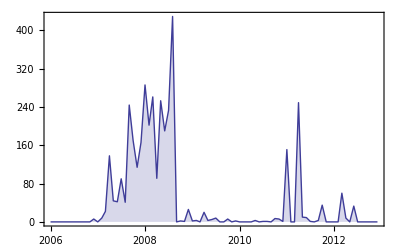

```mathematica
DateListPlot[nrTakenTime,Joined->True,PlotRange->All,Filling->Axis,GridLines->None]
```

## Camera models

```mathematica
getData[goodFileNames[[1]],"Camera"]
```

{Canon,Canon EOS Kiss Digital N}

```mathematica
imageCameras=Monitor[
Table[getData[goodFileNames[[i]],"Camera"],{i,Length[goodFileNames]}],
Refresh[
ProgressIndicator[i,{0,Length[goodFileNames]}],
UpdateInterval->0.5,
TrackedSymbols->{}
]
];
```

```mathematica
{cameraLabel,cameraData}=Transpose@Tally@imageCameras
```

{{{Canon,Canon EOS Kiss Digital N},{Sony Ericsson,K800i},{Canon,Canon EOS 40D},{NIKON CORPORATION,NIKON D3000},{Canon,Canon EOS 650D}},{2517,1074,4,66,25}}

```mathematica
formatLabel[{"Canon","Canon EOS Kiss Digital N"}]="Canon 350D";
formatLabel[{"Sony Ericsson","K800i"}]="Sony Ericsson K800i";
formatLabel[{"Canon","Canon EOS 40D"}]="Canon 40D";
formatLabel[{"NIKON CORPORATION","NIKON D3000"}]="Nikon D3000";
formatLabel[{"Canon","Canon EOS 650D"}]="Canon 650D";
```

```mathematica
PieChart[cameraData,ChartLabels->Placed[formatLabel/@cameraLabel,"RadialCallout"],ImagePadding->50,SectorOrigin->π 10.1/5]
```

-Graphics-

```mathematica
PieChart[cameraData,ChartLegends->formatLabel/@cameraLabel]
```

-Graphics--Graphics- | Canon 350D
-Graphics- | Sony Ericsson K800i
-Graphics- | Canon 40D
-Graphics- | Nikon D3000
-Graphics- | Canon 650D

## Aperture

## Bit depth

## Color space

## Time of day taken

## Exposure

## Focal length

## Image size

## ISO

## Image colors over time

## Memory used

```mathematica
Total@fileSizes[[All,2]]
```

6114153844

## Problematic

## Orientations [weird data]

```mathematica
imageOrientations=Monitor[
Table[getData[goodFileNames[[i]],"Orientation"],{i,Length[goodFileNames]}],
Refresh[
ProgressIndicator[i,{0,Length[goodFileNames]}],
UpdateInterval->0.5,
TrackedSymbols->{}
]
];
```

```mathematica
{orientLabel,orientNr}=Transpose@Tally[Cases[imageOrientations,Except[None]]]
```

{{Right,Top,Left},{5,1798,9}}

```mathematica
PieChart[orientNr,ChartLabels->orientLabel]
```

-Graphics-

## Flash [no data]